# Play Around with Graphics Stacking

## Preparation for PSTH

## Test graphs

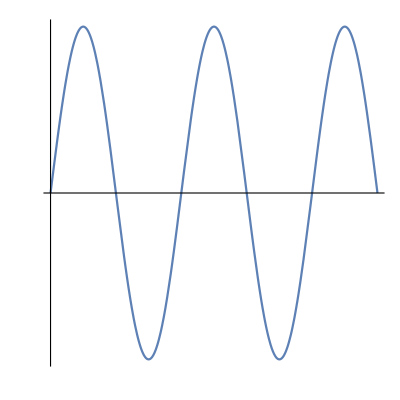

```mathematica
gr1=Plot[Sin[x],{x,0,5Pi},AspectRatio->1,Ticks->None,PlotRangePadding->1,ImageMargins->10]
```

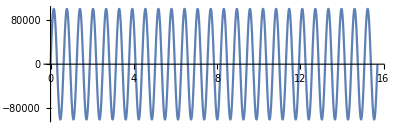

```mathematica
gr2=Plot[100000*Sin[x*10],{x,0,5Pi},AspectRatio->1/3]
```

## Graphics Column?

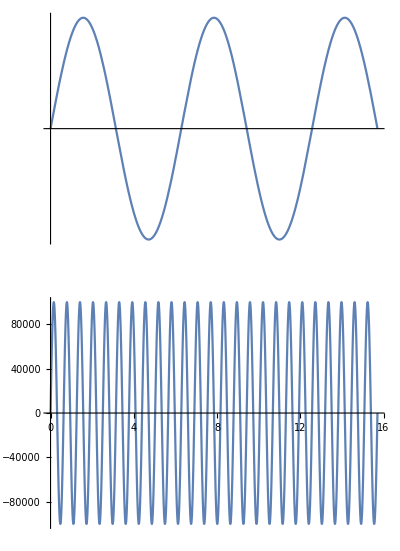

```mathematica
GraphicsColumn[{gr1, gr2}]
```

## Absolute Options

```mathematica
Options[gr1]
```

{DisplayFunction→Identity,AspectRatio→1,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,0},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],Method→{DefaultBoundaryStyle→Automatic,ScalingFunctions→None},PlotRange→{{0,5 π},{-1.,0.999999}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

```mathematica
AbsoluteOptions[gr1]
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

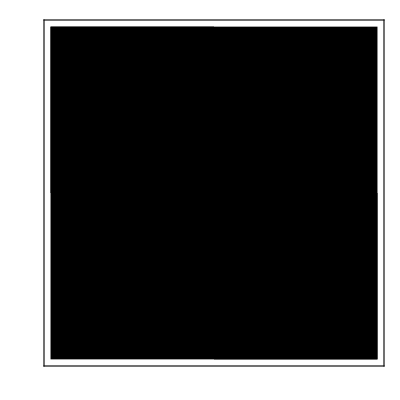
```mathematica
{AlignmentPoint->Center,AspectRatio->1.,Axes->{True,True},AxesLabel->{None,None},AxesOrigin->{0.,0.},AxesStyle->{{-Graphics-,AbsoluteThickness[0.25]},{-Graphics-,AbsoluteThickness[0.25]}},Background->None,BaselinePosition->Automatic,BaseStyle->{},ColorOutput->Automatic,ContentSelectable->Automatic,CoordinatesToolOptions->Automatic,DisplayFunction->Identity,Epilog->{},FormatType->TraditionalForm,Frame->{False,False,False,False},FrameLabel->{{None,None},{None,None}},FrameStyle->{None,None,None,None},FrameTicks->{{},{},{},{}},FrameTicksStyle->{},GridLines->{{},{}},GridLinesStyle->Directive[-Graphics-],ImageMargins->0.,ImagePadding->All,ImageSize->Automatic,ImageSizeRaw->Automatic,LabelStyle->{},Method->{"DefaultBoundaryStyle"->Automatic,"ScalingFunctions"->None},PlotLabel->None,PlotRange->{{0.,15.707963267948966},{-0.9999995448876328,0.9999994330749562}},PlotRangeClipping->True,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},PlotRegion->Automatic,PreserveImageOptions->Automatic,Prolog->{},RotateLabel->True,Ticks->{{},{}},TicksStyle->{}}
```

```mathematica
AbsoluteOptions[FullGraphics[gr1]]
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

```mathematica
{AlignmentPoint->Center,AspectRatio->0.12732388940859388,Axes->{False,False},AxesLabel->None,AxesOrigin->{0.,0.},AxesStyle->{None,None},Background->None,BaselinePosition->Automatic,BaseStyle->{},ColorOutput->Automatic,ContentSelectable->Automatic,CoordinatesToolOptions->Automatic,DisplayFunction->Identity,Epilog->{},FormatType->TraditionalForm,Frame->{False,False,False,False},FrameLabel->None,FrameStyle->{{},{},{},{}},FrameTicks->{None,None,None,None},FrameTicksStyle->{},GridLines->{{},{}},GridLinesStyle->{},ImageMargins->0.,ImagePadding->All,ImageSize->Automatic,ImageSizeRaw->Automatic,LabelStyle->{},Method->Automatic,PlotLabel->None,PlotRange->{{0.,15.707963267948966},{-0.9999995448876328,0.9999994330749562}},PlotRangeClipping->False,PlotRangePadding->Automatic,PlotRegion->Automatic,PreserveImageOptions->Automatic,Prolog->{},RotateLabel->True,Ticks->{{{0.,0.,{0.00625,0.},{-Graphics-,AbsoluteThickness[0.25]}},...{0.95,"",{0.00375,0.},{-Graphics-,AbsoluteThickness[0.125]}}}},TicksStyle->{}}
```

## Inset

```mathematica
<<HokahokaW`
```

HokahokaW`
(origin)[https://github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  d53abeb24d474c8cf373080d76c6b138bb9bee5c
newest file:  Mon 15 Sep 2014 22:48:41

```mathematica
gr1AR=HHOptionValue(*HHAbsoluteOptionValue*)[gr1, AspectRatio]
```

1

```mathematica
gr1PR=HHOptionValue(*HHAbsoluteOptionValue*)[gr1, PlotRange]
```

{{0,5 π},{-1.,0.999999}}

```mathematica
Dimensions[gr1PR]
```

{2,2}

```mathematica
grSize=HHAbsoluteOptionValue[gr1, PlotRange]
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

{{0.,15.708},{-1.,0.999999}}

```mathematica
HHOptionValue[Image[({{0.1, 0.2, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})],PlotRange]
```

OptionValue::optnf: Option name PlotRange not found in defaults for {ColorSpace → Automatic, Interleaving → None, AlignmentPoint → Center, BaselinePosition → Automatic, ColorSpace → Automatic, ImageResolution → Automatic, ImageSize → Automatic, Interleaving → Automatic, Magnification → Automatic, MetaInformation → {}, TaggingRules → {}}.

PlotRange

```mathematica
grSize=HHAbsoluteOptionValue[gr1, ImageSize]
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

Automatic

```mathematica
grSize=HHAbsoluteOptionValue[gr1, ImageSizeRaw]
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

Automatic

```mathematica
gr1PRP=HHOptionValue(*HHAbsoluteOptionValue*)[gr1, PlotRangePadding]
```

{{1,1},{1,1}}

```mathematica
gr1PRP=HHAbsoluteOptionValue[gr1, PlotRangePadding]
```

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

Axes::axes: {{False, False}, {False, False}} is not a valid axis specification.

General::stop: Further output of Axes :: axes will be suppressed during this calculation.

Ticks::ticks: {Automatic, Automatic} is not a valid tick specification.

General::stop: Further output of Ticks :: ticks will be suppressed during this calculation.

{{1.,1.},{1.,1.}}

```mathematica
gr2AR=HHOptionValue(*HHAbsoluteOptionValue*)[gr2, AspectRatio]
```

1/3

```mathematica
gr2PRP=HHOptionValue(*HHAbsoluteOptionValue*)[gr2, PlotRangePadding]
```

{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}}

```mathematica
Options[Inset]
```

{Alignment→Left,Background→None,BaseStyle→Inset,ContentSelectable→Automatic,FormatType→Automatic}

```mathematica
Show[gr1,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}}]
```

-Graphics-

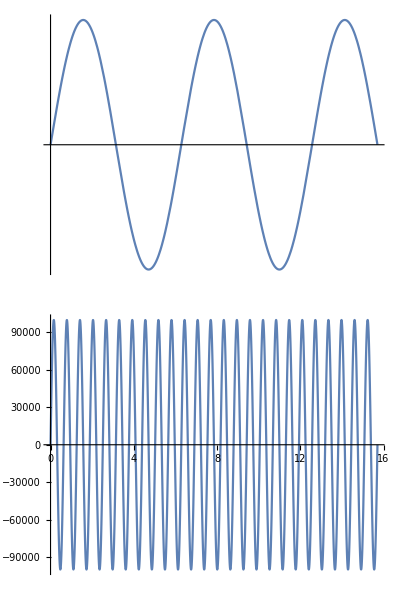

```mathematica
Graphics[{
Inset[Show[gr2,PlotRangePadding->{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}}],{0, 0},{Left, Bottom}, 100],
Inset[gr1,{0, 100*gr2AR},{Left, Bottom}, 100]},
PlotRange->{{0,100},{0,100*gr2AR+100*gr1AR}}
]
```

```mathematica
HHGraphicsColumn[{gr1, gr2}]
```

-Graphics-

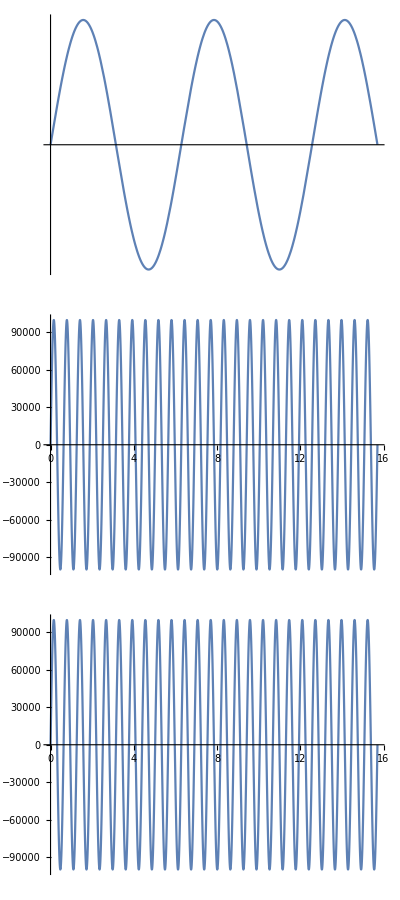

```mathematica
HHGraphicsColumn[{gr1, gr2,gr2}]
```